```mathematica
f:=a^2+b;
a={1,2};
b={2,3};
f
```

{3,7}

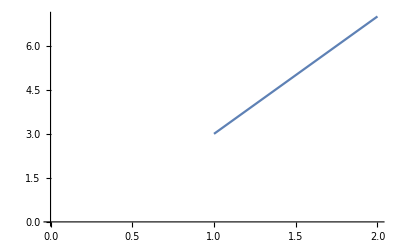

```mathematica
ListLinePlot[f]
```

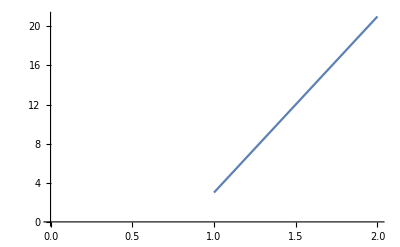

```mathematica
f:=a^2+b;
a={1,4};
b={2,5};
ListLinePlot[f]
```

```mathematica
f:=a^2+b;
a={1,4};
b={2,5};
ListLinePlot[f[#]&/@{2}]
```

-Graphics-

```mathematica
[f[#]&/@{2}]
```

```mathematica
If[1==1,"dope","nope"]
```

dope

```mathematica
a={1,2,3};
b={2,3,5};
```

```mathematica
If[a==b,"hell yeah","hell nah"]
```

hell nah

```mathematica
Array[If[#1==#2,1,0]&,{5,5}]//Grid
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

```mathematica
a=10;
b=4;
Array[If[#1+2==#2,1,0]&,{a,a}]//Grid
```

0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
*define a function and apply it to every value in an array*
```

```mathematica
testFunct[x_]:=If[x<3,1,0]
```

```mathematica
testFunct[2]
```

1

```mathematica
testFunct[4]
```

0

```mathematica
a={1,2,3,4};
testFunct/@a
```

{1,1,0,0}

```mathematica
a
b
```

{1,2,3,4}

```mathematica
4

*difference between adding, multiplying, and taking dot product*
```

```mathematica
a={1,2,3};
b={1,2,3};
a+b
a*b
a.b
```

{2,4,6}

{1,4,9}

14

```mathematica
a={{1,2,3},{4,5,6},{7,8,9}};
b={{1,2,3},{4,5,6},{7,8,9}};
a+b//Grid
a*b//Grid
a.b//Grid
```

2 | 4 | 6
8 | 10 | 12
14 | 16 | 18

1 | 4 | 9
16 | 25 | 36
49 | 64 | 81

30 | 36 | 42
66 | 81 | 96
102 | 126 | 150

```mathematica
FullForm[2^9]
```

512

```mathematica
Array[1,9]
```

{1[1],1[2],1[3],1[4],1[5],1[6],1[7],1[8],1[9]}

```mathematica
f=1;
Array[f,{1,9}]
```

{{1[1,1],1[1,2],1[1,3],1[1,4],1[1,5],1[1,6],1[1,7],1[1,8],1[1,9]}}

```mathematica
Table[1,{1,10}]
```

Table::itraw: Raw object 1 cannot be used as an iterator.

```mathematica
Table[2,3,10]
```

{{2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2},{2,2,2,2,2,2,2,2,2,2}}

```mathematica
Table[i^2,{i,5}]
```

{1,4,9,16,25}

```mathematica
a=Table[i*j,{i,2},{j,3}]//Grid;
b=Transpose[a,];
a
b
```

1 | 2 | 3
2 | 4 | 6

```mathematica
Transpose[{{1, 2, 3}, {2, 4, 6}}]
```

```mathematica
a={1,2,3};
b={1,2,3};
x={{a},{b}}//Grid;
y=Transpose[x];
x
y
```

{1,2,3}
{1,2,3}

Transpose[{1,2,3}
{1,2,3}]

```mathematica
Transpose[{{a,b,c},{x,y,z}}]
```

{{{1,2,3},{1,2,3}
{1,2,3}},{{1,2,3},Transpose[{1,2,3}
{1,2,3}]},{c,z}}

```mathematica
a={};
```

```mathematica
b={};
```

```mathematica
Transpose[{{a,b,c},{x,y,z}}]
```

{{{},{1,2,3}
{1,2,3}},{{},Transpose[{1,2,3}
{1,2,3}]},{c,z}}

```mathematica
x={};
y={};
```

```mathematica
Transpose[{{a,b,c},{x,y,z}}]
```

{{{},{}},{{},{}},{c,z}}

```mathematica
Transpose[{{1,2,3},{4,5,6}}]//Grid
```

```mathematica
{{1, 4}, {2, 5}, {3, 6}}



*This wasn't  working b/c syntax*
*Transpose needs arguments in array format, so {{a},{b},{c}} will work. other list forms won't*
```

```mathematica
a={1,2,3};
b={4,5,6};
x=Transpose[{a,b}]//Grid
y={a,b}//Grid
```

1 | 4
2 | 5
3 | 6

1 | 2 | 3
4 | 5 | 6

```mathematica
x={a,b}
```

{{1,2,3},{4,5,6}}

```mathematica
Transpose[x]//Grid
```

1 | 4
2 | 5
3 | 6

```mathematica
Table[1/i,{i,10}]
```

```mathematica
{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

*x={} does NOT clear x. Have to use Clear[x] for that.*
```

```mathematica
Clear[f]
f[x_]:=1/x
x=Range[10]
f/@x
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}


*question 1*
```

```mathematica
Clear[x]
isNegative[x_]:=If[x<0,"True","False"];
x={-3,-2,-1,0,1,2};
isNegative/@x
```

```mathematica
{"True","True","True","False","False","False"}


*question 2*
```

```mathematica
f[n_]:=Range[n];
n=5;
f[n]
n=7;
f[n]
n=Range[7];
f/@n//Grid
```

{1,2,3,4,5}

{1,2,3,4,5,6,7}

```mathematica
{{1, , , , , , }, {1, 2, , , , , }, {1, 2, 3, , , , }, {1, 2, 3, 4, , , }, {1, 2, 3, 4, 5, , }, {1, 2, 3, 4, 5, 6, }, {1, 2, 3, 4, 5, 6, 7}}


*question 3*
```

```mathematica
num7=0;
f[x_]:=If[x==7,num7=num7+1,num7=num7];
x={1,7,3,7,8,6,7,1,3,3,7};
count=f/@x;
Max[count]
```

4

```mathematica
*question 4*
```

```mathematica
f[a_,b_]:=If[a==b,"true","false"]
a={1,2,4};
b={1,2,3};
f[a,b]
```

false

```mathematica
*question 5*
```

```mathematica
f[m_]:=If[0<m≤25,A,If[25<m≤50,B,If[50<m≤75,C,If[75<m≤100,D,0]]]]
m=RandomReal[100,20];
f/@m
```

{D,A,C,A,B,A,C,C,A,D,B,D,D,D,B,D,C,D,A,A}

```mathematica
*alternative method for 5*
```

```mathematica
f[m_]:=If[m≤50,If[m≤25,A,B],If[m≤75,If[m≤100,C,D]]]
m=RandomReal[100,20];
f/@m
```

{C,A,C,C,C,A,Null,C,A,Null,Null,A,A,B,Null,C,C,Null,Null,A}

```mathematica
*question 6*
```

```mathematica
f[m_]:=If[m≤0,"Failed",If[0<m≤25,A,If[25<m≤50,B,If[50<m≤75,C,If[75<m≤100,D,"Failed"]]]]]
m=RandomReal[{-50,150},20];
f/@m
```

{Failed,A,A,Failed,Failed,Failed,D,A,A,Failed,A,Failed,B,Failed,Failed,Failed,Failed,D,D,D}